```mathematica
DApprox[j_]:=(-1)^j+Sum[(-1)^(j-k+1)/(k!) n (Log[n])^k,{k,0,j-1}]
```

```mathematica
DApprox[j]
```

(-1)^j-((-1)^j Gamma[j,-Log[n]])/Gamma[j]

```mathematica
FF[n_,j_] := (-1)^j-((-1)^j Gamma[j,-Log[n]])/Gamma[j]
```

```mathematica
FF[n,-1]
```

-1

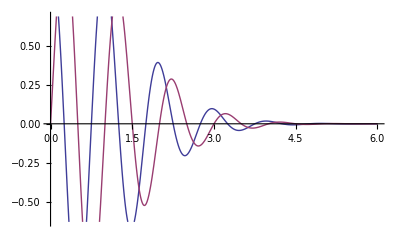

```mathematica
Plot[{Re[FF[2,j]],Im[FF[2,j]]},{j,0,6}]
```

```mathematica
FF2[n_,j_] := (((-1)^j-((-1)^j Gamma[j,-Log[n]])/Gamma[j])-1)/j
```

```mathematica
Expand[FF2[n,0.0000000000000001]]
```

(0.+3.14159 ⅈ)-(1.+3.14159×10^-16 ⅈ) Gamma[1.×10^-16,-Log[n]]

```mathematica
FF3a[n_] := -Gamma[0,-Log[n]]
```

```mathematica
FF3a[n]
```

-Gamma[0,-Log[n]]

```mathematica
N[FF3a[a=100]]
N[LogIntegral[a]]
```

30.1261+3.14159 ⅈ

30.1261

30.1261

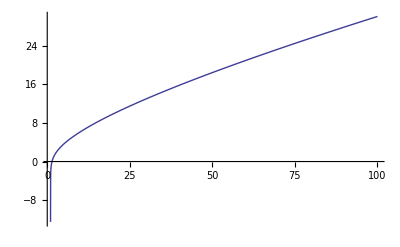

```mathematica
Plot[Re[-Gamma[0,-Log[n]]],{n,1,100}]
```

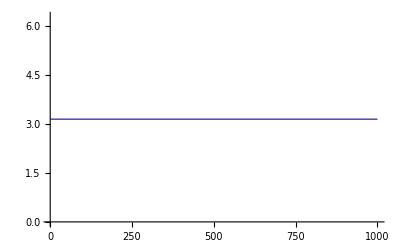

```mathematica
Plot[Im[1-Gamma[0,-Log[n]]],{n,1,1000}]
```

```mathematica
-Gamma[0,-n]
```

-Gamma[0,-n]

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
F4[n_,z_] := Sum[
```

```mathematica
FullSimplify[(1/Gamma[z])(1/z)]
```

1/Gamma[1+z]

```mathematica
1/Gamma[1+0]
```

1